```mathematica
g[y_]:={{1,0},{0,1+(z'[y])^2}}
```

```mathematica
detg[y_]:=Det[g[y]]
```

```mathematica
sqrtdetg[y_]:=Sqrt[detg[y]]
```

```mathematica
H[y_]:=1/2/( detg[y])^(3/2)z''[y]
```

```mathematica
Derivative[1][detg][y]
```

2 z'[y] z''[y]

```mathematica
σ[y_]:=σ0
```

```mathematica
L=10;
h=1;
κ=1;
σ0=1;
CC=1/100;
```

```mathematica
eq={κ(-(1/sqrtdetg[y])D[H'[y]/sqrtdetg[y],y]-2( H[y])^3)+ σ [y]H[y]==0}//FullSimplify
```

{((5-30 z'[y]^2) z''[y]^3+2 (1+z'[y]^2) z''[y] ((1+z'[y]^2)^2+10 z'[y] z^(3)[y])-2 (1+z'[y]^2)^2 z^(4)[y])/(√(1+z'[y]^2))==0}

```mathematica
bcs={z[0]==0,z[h]==CC,z'[0]==0,z'[h]==CC}
```

{z[0]==0,z[1]==1/100,z'[0]==0,z'[1]==1/100}

```mathematica
sys=Flatten[{eq,bcs}]
```

{((5-30 z'[y]^2) z''[y]^3+2 (1+z'[y]^2) z''[y] ((1+z'[y]^2)^2+10 z'[y] z^(3)[y])-2 (1+z'[y]^2)^2 z^(4)[y])/(√(1+z'[y]^2))==0,z[0]==0,z[1]==1/100,z'[0]==0,z'[1]==1/100}

```mathematica
sol=NDSolve[sys,z,{y,0,h},WorkingPrecision->10]
```

{{z→InterpolatingFunction[…]}}

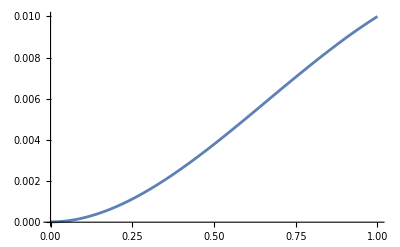

```mathematica
plotexact=Plot[Evaluate[z[y]/.sol],{y,0,h},PlotRange->All]
```

```mathematica
t=Import["~/Documents/finite_elements/solution/z.csv"];
t=Table[{t[[i,3]],If[Abs[t[[i,2]]-L/2]<0.1,t[[i,1]],0]},{i,2,Length[t]}]
```

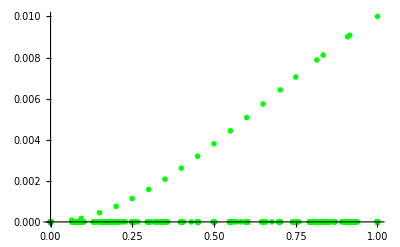

```mathematica
plotnum=ListPlot[t,PlotStyle->{Green,PointSize->0.01}]
```

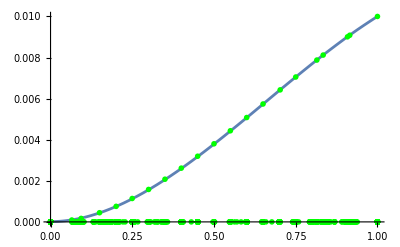

```mathematica
Show[plotexact,plotnum]
```